```mathematica
Clear["Global`*"]
```

Read raw data from experiment HDF5 files. Find the probabilities according to a maximum likelihood optimizer.

## Input

```mathematica
darkprobred = {55,67,59,57,59,52,44,49,44};
brightprobred = {55,74,73,78,75,89,82,75,84};

darkprobblue = {55,67,59,57,59,52,44,49,44};
brightprobblue = {55,74,73,78,75,89,82,75,84};

freqdetred = 0;
freqstepred = 0;

freqdetblue = 0;
freqstepblue = 0;
```

## Logic

### Fit Frequency Scan

```mathematica
Pup[A_, Ω0_,ω_,ω0_] := A Ω0^2/(Ω0^2+(ω-ω0)^2) Sin[(√(Ω0^2+(ω-ω0)^2)π)/(2 Ω0)]^2;
RabiFit=Table[NonlinearModelFit[oneionbrightM[[i]],Pup[A0,Ω0,ω,ω0],{{A0,0},{Ω0,Ω0approx},{ω0,freqapprox}},ω],{i,1,Length[oneionbrightM]}];
```

## Output

```mathematica
probabilities = Probs[onebright, twobright]*100;
```

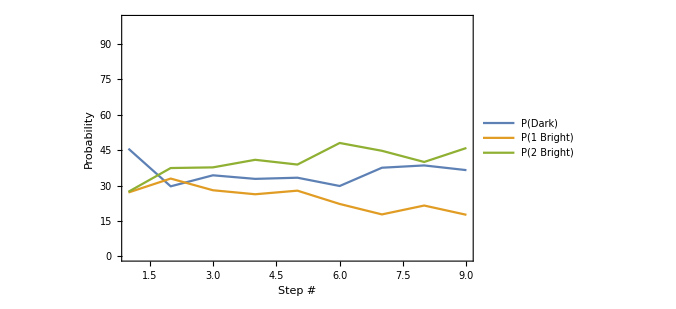

```mathematica
ListLinePlot[Transpose[probabilities], Frame-> True, ImageSize-> 500, PlotRange->{All,{0, 100}},  FrameLabel-> {"Step #", "Probability"}, FrameStyle->{Bold, Black}, LabelStyle->16, PlotLegends->{"P(Dark)", "P(1 Bright)", "P(2 Bright)"}]
```